# Lagrange Interpolation method

```mathematica
n=11;  h=0.5; a=3;
x=Table[a+(i-1) h,{i,1,n}];
f:=Log[10,#]&
y=Table[f[x[[i]]],{i,1,n}];
xydata=Table[{x[[i]],y[[i]]},{i,n}];
Style[Grid[xydata, Alignment -> Left, Spacings -> {2, 1}, Frame->All],Large]
```

3. | 0.477121
3.5 | 0.544068
4. | 0.60206
4.5 | 0.653213
5. | 0.69897
5.5 | 0.740363
6. | 0.778151
6.5 | 0.812913
7. | 0.845098
7.5 | 0.875061
8. | 0.90309

## Lagrange Interpolation Polynom

Function

```mathematica
LagrangeInterpolationPolynom[x_,y_,z_]:=Module[{n,k,i,Dn=Table[1,{i,n}],PN,Pn=Table[1,{i,n}],h=x[[2]]-x[[1]]},
n=Length[x];
For [i=1,i≤n,i++,
For[ k=1,k≤n,k++,
If [k≠i,Pn[[i]]*=z-x[[k]];
Dn[[i]]*=x[[i]]-x[[k]]
]
]
];
PN=Pn[[1]]*y[[1]]/Dn[[1]];
For [k=1,k≤n-1,k++,
 PN+=Pn[[k+1]]*y[[k+1]]/Dn[[k+1]]
];
PN
]
```

Calculates

2.54384×10^-16

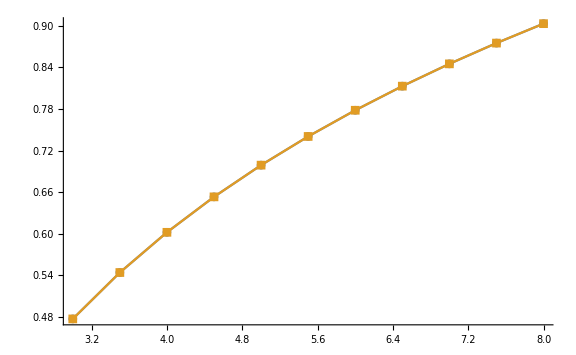

```mathematica
yLagrangeInterpolation=Table[LagrangeInterpolationPolynom[x,y,x[[i]]],{i,n}];
dataLagrangeInterpolation=Table[{x[[i]],yLagrangeInterpolation[[i]]},{i,n}];
qatelik=Norm[yLagrangeInterpolation-y]
Show[ListLinePlot[{xydata,dataLagrangeInterpolation},PlotMarkers->Automatic],ImageSize->Large]
```

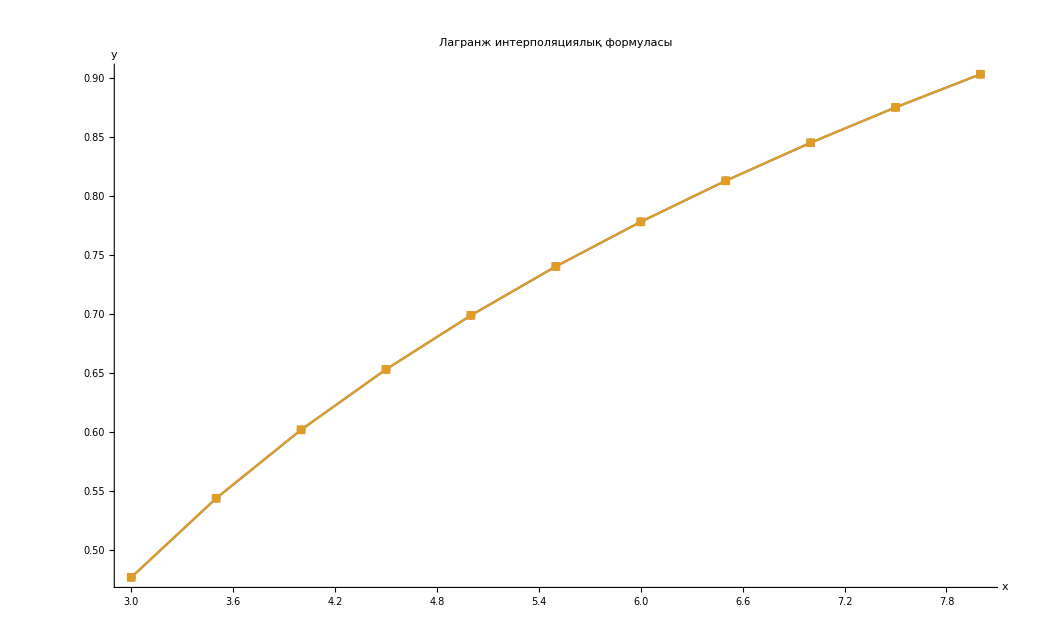

```mathematica
Show[%120,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[Лагранж интерполяциялық формуласы],LabelStyle->{22,RGBColor[0.5000076295109483,0.,0.5000076295109483]}]
```